# Recursividad

## Carga de librería

```mathematica
<< Vilcretas`
```

VilCretas está disponible.

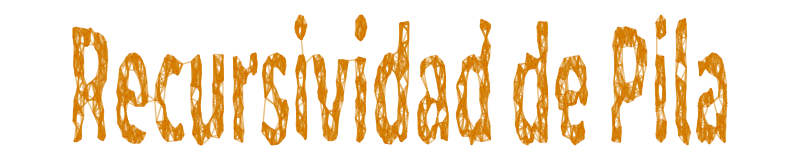

```mathematica
GrafoString["Recursividad de Pila"]
```

```mathematica
FactorialPropio[n_] := If[n <= 1, 1, n *FactorialPropio[n - 1]]
```

```mathematica
FactorialPropio[5]
```

120

```mathematica
SumatoriaPropia[init_, fin_]:= If[init == fin, fin, init + SumatoriaPropia[init + 1, fin]]
```

```mathematica
SumatoriaPropia[0, 5]
```

15

```mathematica
PotenciaDeUnNumero[a_, b_] := If[b == 0, 1, a * PotenciaDeUnNumero[a, b - 1]]
```

```mathematica
PotenciaDeUnNumero[2,8]
```

256

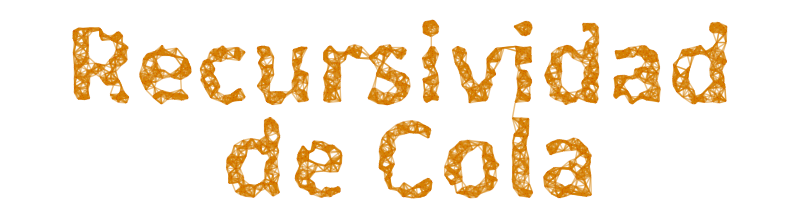

```mathematica
GrafoString["Recursividad de Cola"]
```

```mathematica
FactorialCola[n_]:=Module[{funcAux},funcAux[x_,acc_]:=If[x==0,acc,funcAux[x-1,x*acc]];
funcAux[n,1]]
```

```mathematica
FactorialCola[5]
```

120

```mathematica
FibonacciCola[n_]:=Module[{funcAux},funcAux[x_,a_,b_]:=If[x==0,a,funcAux[x-1,b,a+b]];
funcAux[n,0,1]]
```

```mathematica
FibonacciCola[10]
```

55

```mathematica
PotenciaCola[a_,b_]:=Module[{funcAux},funcAux[x_,y_,acc_]:=If[y==0,acc,funcAux[x,y-1,acc*x]];
funcAux[a,b,1]]
```

```mathematica
PotenciaCola[2, 8]
```

256

```mathematica
MCDPropio[a_,b_]:=If[b==0,a,MCDPropio[b,Mod[a,b]]]
```

```mathematica
MCDPropio[48, 18]
```

6

```mathematica
Manipulate[Column[{"### Recursividad de Pila ###",DynamicModule[{stepsPila={}},Module[{factorialPila},factorialPila[x_]:=(AppendTo[stepsPila,"Llamada factorialPila["<>ToString[x]<>"]"];
If[x==0,1,Module[{result=x*factorialPila[x-1]},AppendTo[stepsPila,"Resultado factorialPila["<>ToString[x]<>"] = "<>ToString[result]];
result]]);
{factorialPila[n],Column[stepsPila]}]],Spacer[10],"### Recursividad de Cola ###",DynamicModule[{stepsCola={}},Module[{factorialCola},factorialCola[x_,acc_]:=(AppendTo[stepsCola,"Llamada factorialCola["<>ToString[x]<>", "<>ToString[acc]<>"]"];
If[x==0,acc,factorialCola[x-1,x*acc]]);
{factorialCola[n,1],Column[stepsCola]}]]}],{{n,5},0,10,1,Appearance->"Labeled"}]
```